# 12.010 HW 4 2011

### This latest version of Mathematica has some issues with copying and pasting equations and graphics from Microsoft Word. It also seems not to be able to reproduce subscripts and superscripts from word, which previously was able to do. It is not clear if the incompatibility is from the Microsoft Word or the Mathematica side. This is another indication of how changes in versions of software can have unintended consequences.

## (Question 1): (25-points) (a) Write Mathematica NoteBook which generates a table of error function (erf) and its derivatives for real arguments (z) between -3 and 3 in steps of 0.25. The error function is defined by the equation below (but is rarely evaluated by performing the integration). (see http://mathworld.wolfram.com/Erf.html for information the error function ) The values in the table should be given with 5 decimal places. The table should have headers explaining what the columns are. Explain how you designed the NoteBook and give an example of the output. (b) How would you change this NoteBook if 10 significant digits were required? Mathematica NoteBook should also be supplied

Solution: Given that the error function is defined in Mathematica themost tricky part of the this problem is formarting the ourput.  There are many ways to approach the output problem.

```mathematica
Off[General::spell1];  (* Stops message about head looking like a command*)
head={"Argument","Erf[z]","dErf[z]/dz"};
derf[arg_] := 2/Sqrt[Pi]*Exp[-x^2];
ents=Table[{N[SetAccuracy[x,10],3],N[SetAccuracy[Erf[x],10],6],N[SetAccuracy[derf[x],6],6]},{x,-3,3,0.25}];
full=Insert[ents,head,1];
TableForm[full,TableAlignments->Right]
```

Argument | Erf[z] | dErf[z]/dz
-3. | -0.999978 | 0.00014
-2.75 | -0.999899 | 0.00059
-2.5 | -0.999593 | 0.00218
-2.25 | -0.998537 | 0.00714
-2. | -0.995322 | 0.02067
-1.75 | -0.986672 | 0.05277
-1.5 | -0.966105 | 0.11893
-1.25 | -0.9229 | 0.23652
-1. | -0.842701 | 0.41511
-0.75 | -0.711156 | 0.64293
-0.5 | -0.5205 | 0.87878
-0.25 | -0.276326 | 1.06001
0. | 0. | 1.12838
0.25 | 0.276326 | 1.06001
0.5 | 0.5205 | 0.87878
0.75 | 0.711156 | 0.64293
1. | 0.842701 | 0.41511
1.25 | 0.9229 | 0.23652
1.5 | 0.966105 | 0.11893
1.75 | 0.986672 | 0.05277
2. | 0.995322 | 0.02067
2.25 | 0.998537 | 0.00714
2.5 | 0.999593 | 0.00218
2.75 | 0.999899 | 0.00059
3. | 0.999978 | 0.00014

(b) Output of table to 10 deciminal places.

```mathematica
Off[General::spell1];  (* Stops message about head looking like a command*)
head={"Argument","Erf[z]","dErf[z]/dz"};
derf[arg_] := 2/Sqrt[Pi]*Exp[-x^2];
ents=Table[{N[SetAccuracy[x,10],3],N[SetAccuracy[Erf[x],10],10],N[SetAccuracy[derf[x],10],10]},{x,-3,3,0.25}];
full=Insert[ents,head,1];
TableForm[full,TableAlignments->Right]
```

Argument | Erf[z] | dErf[z]/dz
-3. | -0.99997791 | 0.000139253
-2.75 | -0.999899378 | 0.000586277
-2.5 | -0.999593048 | 0.002178284
-2.25 | -0.998537283 | 0.007142319
-2. | -0.995322265 | 0.020666985
-1.75 | -0.986671671 | 0.052774996
-1.5 | -0.966105146 | 0.118930289
-1.25 | -0.922900128 | 0.236521122
-1. | -0.842700793 | 0.415107497
-0.75 | -0.711155634 | 0.642931069
-0.5 | -0.520499878 | 0.878782579
-0.25 | -0.27632639 | 1.060014129
0. | 0. | 1.128379167
0.25 | 0.27632639 | 1.060014129
0.5 | 0.520499878 | 0.878782579
0.75 | 0.711155634 | 0.642931069
1. | 0.842700793 | 0.415107497
1.25 | 0.922900128 | 0.236521122
1.5 | 0.966105146 | 0.118930289
1.75 | 0.986671671 | 0.052774996
2. | 0.995322265 | 0.020666985
2.25 | 0.998537283 | 0.007142319
2.5 | 0.999593048 | 0.002178284
2.75 | 0.999899378 | 0.000586277
3. | 0.99997791 | 0.000139253

## Question (2): (25-points). Write a NoteBook that reads your name in the form <first name> <middle name> <last name> and outputs the last name first and adds a comma after the name, the first name, and initial of your middle name with a period after the middle initial. If the names start with lower case letters, then these should be capitalized. The NoteBook should not be specific to the lengths of your name (ie., the NoteBook should work with anyone’s name. As an example. An input of thomas abram herring would generate: Herring, Thomas A.

This problem is not too bad to solve.  This solution works in >5.0 Mathematica and does explicitly some things such as splitting a string apart that are now Mathematica commands (StringSplit).

```mathematica
(* Define a function that will convert chararacter of a string to upper case *)
confirst[a_] := StringReplacePart[a,ToUpperCase[StringTake[a,{1}]],{1,1}];
(* Get the name from the user*)
inname = InputString["Enter Name (first, middle, last) "]; 
(* Convert whole string to lower case*)
fullname = ToLowerCase[inname];
(* Now get the list of blanks in the string*)
posblanks = StringPosition[fullname," "];
(* Get the position of first blank*)
posfirst = Extract[Extract[posblanks,1],1];
firstname = StringTake[fullname,posfirst-1];
firstname = confirst[firstname];  (* Use our confirst routine *)
(* Get Middle Name *)
posmid = Extract[Extract[posblanks,2],1];
midinit = StringTake[fullname,{posfirst+1, posfirst+1}];
midinit = confirst[midinit];
(* Get Last Name *)
lastname = StringTake[fullname,{posmid+1,StringLength[fullname]}];
lastname = confirst[lastname];
(* Output the string *)
finalname = lastname <> ", " <> firstname <> " " <> midinit <> ".";
outline = "Input name " <> inname <> " converted to: " <> finalname;
(* Output the results*)
Print[outline];
```

Input name thomas abram herring converted to: Herring, Thomas A.

## Write a Mathematica NoteBook that will compute the motion of a bicyclist and the energy used cycling along an oscillating, sloped straight-line path. The path followed will be expressed as where H(x) is the height of the path above the starting height, S is a slope in m/m, A and B are amplitudes of sinusoidal oscillations in the path. The wavelength of the oscillations is λ. The forces acting on the bicycle are: where Ar is the cross-sectional area of the rider, Cd is the drag coefficient, r is the density of air and V is the velocity of the bike. For the rolling drag, Mr is the mass of the rider and bike, g is gravitation acceleration and Cr is rolling drag coefficient. The bicyclist puts power into the bike by pedaling. The force generated by this power is given by where Fr is the force produced by the rider, Pr is power used by the rider and V is velocity that the bike is traveling (the force is assumed to act along the velocity vector of the bike). Your NoteBook can assume that the power can be used at different rates along the path. The energy used will be the integrated power supplied by the rider. Assume that there is maximum value to the rider force. Your code should allow for input of the constants above (path and force coefficients). The NoteBook can assume a constant power scenario and constant force at low velocities. As a test of your NoteBook use the following constants to compute: (a) Time to travel and energy used to travel 10 km along a path specified by S=0.001, A=5.0 m, B=0.0 m and λ= 2km, with constant power use of Pr =100Watts and a maximum force available of 20N. (b) The position and velocity of the bike tabulated at a 100-second interval. (c) Add graphics to your NoteBook which plots the velocity of the bike as a function of time and position along the path. Assume the following values Cd = 0.9 Cr = 0.007 Ar = 0.67 m2 ρ = 1.226 kg/m3 g = 9.8 m/s2 Mr = 80 kg In this case, the Mathematica NoteBook will not be of the type used for fortran and C/C++. Look at the documentation on NDSolve for this problem. Your answer to this question should include: (a) The algorithms used and the design of your NoteBook (b) The Mathematica NoteBook with your code and solution (I run your NoteBook). (c) The results from the test case above.

There are several ways of approaching this problem and two solution are presented below.  The problem itself is dvided into a number of cells that allow parts of problem to be re-execuated.  There two basic steps to the solution:
(1) Use NDSolve to solve the second order differential equation that describes the problem.  The solution effectively becomes an equation that returns values at any specified time.
(2) Use FindRoot to determine when the bike has reached the end of track.

Set up the defaults first.  This cell should be evaluated

```mathematica
Clear[t,x, xd,  hx, vx, xp, xd, th, dacc];
cd = 0.90 ;
(*Print["Parameter cd ",cd]*)
cr = 0.007;
area = 0.67;  (* m^2 *)
mass = 80;  (* kg *)
prider = 100;  (* Power Watts*)
fmax = 20;
slope = 0.001;
as = 5.0;
bs = 0.0;
lambda = 2000;
tracklen = 10000;
outint = 100.0;

(* Define the acceleration functions we will need*)
grav = 9.8 ; 
rhoair = 1.226;
Print["Default Values set"]
```

Default Values set

Now allow the user to enter values of there own.  This cell does not need to be evaluated if the default values are desired.

```mathematica
tracklen = Input["Length of track (km) ",tracklen/1000]*1000.0;
slope = Input["Track slope ",slope];
as = Input["Sin Amplitude (m) ",as];
bs = Input["Cos Ampliude (m )",bs];
lambda = Input["Periodic wavelength (km) ",lambda/1000]*1000.0;
mass = Input["Rider+Bike  Mass (kg) ",mass];
area = Input["Rider Area (m^2) ",area];
cd = Input["Drag Coefficient ",cd];
cr = Input["Rolling friction coefficient ",cr];
outint = Input["Output interval (s)",outint];
```

Now set up the force model equations

```mathematica
theta[xp_] := ArcTan[slope + as*Cos[2*Pi*xp/lambda]*2*Pi/lambda - bs*Sin[2*Pi*xp/lambda]*2*Pi/lambda]
htrack[xp_] := slope*xp+as*Sin[2*Pi*xp/lambda]+bs*Cos[2*Pi*xp/lambda];
(* Second derivative of surface for computing cenripical acceleration *)
dy2dx2[xp_] := -as*Sin[2*Pi*xp/lambda]*(2*Pi/lambda)^2-bs*Cos[2*Pi*xp/lambda]*(2*Pi/lambda)^2;
vmag[xd_,zd_] := Sqrt[xd^2+zd^2];

(* Acceleration due to drag *)
dragx[xd_,zd_] := -rhoair*vmag[xd,zd]*area*cd*xd/(2*mass);
dragz[xd_,zd_] := -rhoair*vmag[xd,zd]*area*cd*zd/(2*mass);
(* Rolling force.  This act along surface *)
rollx[xp_] :=  -grav*cr*Cos[theta[xp]];
rollz[xp_] := -grav*cr*Sin[theta[xp]];
(* Gravity force acting perpendicular to surface *)
gravx[xp_] := -grav*Cos[theta[xp]]*Sin[theta[xp]];
gravz[xp_] := +grav*Cos[theta[xp]]^2;
(* Centripetal acceleration *)
(* Could divide by Sqrt[(1+Tan[theta[xp]]^2)^3]] factor to curvature term.  This change does not seem to make solution closer to track shape*)
centx[xp_,xd_,zd_] := (xd^2+zd^2)*Sin[theta[xp]]*dy2dx2[xp];
centz[xp_,xd_,zd_] := (xd^2+zd^2)*Cos[theta[xp]]*dy2dx2[xp]; 
(* This commented code has expression for radius of curvature
centx[xp_,xd_,zd_] := (xd^2+zd^2)*Sin[theta[xp]]*dy2dx2[xp]/Sqrt[(1+Tan[theta[xp]]^2)^3];
centz[xp_,xd_,zd_] := (xd^2+zd^2)*Cos[theta[xp]]*dy2dx2[xp]/Sqrt[(1+Tan[theta[xp]]^2)^3];
*)
(* To see the effects of the centripetal force, remove the comments below
centx[xp_,xd_,zd_] :=0;
centz[xp_,xd_,zd_] :=0;
*)

(* Now the rider force *)
ridrx[xp_,xd_,zd_]  := (Min[If[ vmag[xd,zd]> 0, prider/vmag[xd,zd],fmax], fmax]/mass)*Cos[theta[xp]];
ridrz[xp_,xd_,zd_]  := (Min[If[ vmag[xd,zd]> 0, prider/vmag[xd,zd],fmax], fmax]/mass)*Sin[theta[xp]];
Print[Acceleration functions Set]
```

Acceleration functions Set

The following cell can be used to test that the acceleration functions above generate numeric results when called with distance and velocity.  This test is useful if NDSolve does not return answer.

```mathematica
dx = 1500.; txv = 2.0; tzv = 0.01;
Print["Slope ",theta[dx]," 2nd derivative ", dy2dx2[dx]," Height ",htrack[dx]]
Print["Drag X ",dragx[txv, tzv]," Z ",dragz[txv, tzv]]
Print["Roll X ",rollx[dx]," Z ",rollz[dx]] 
Print["Gravity X ",gravx[dx]," Z ",gravz[dx]] 
Print["Centripetal X ",centx[dx, txv, tzv]," Z ",centz[dx, txv, tzv]]
Print["Rider X ",ridrx[dx, txv, tzv]," Z ",ridrz[dx, txv, tzv]]
```

Slope 0.001 2nd derivative 0.000049348 Height -3.5

Drag X -0.0184822 Z -0.0000924109

Roll X -0.0686 Z -0.0000686

Gravity X -0.00979999 Z 9.79999

Centripetal X 1.97397×10^-7 Z 0.000197397

Rider X 0.25 Z 0.00025

Now set up the solution for NDSolve.  There are two equations in the x and z accelerations and initial conditions for x and z and x' and z' at time zero.  The solution is set to solve for a maximum of 10000 seconds.  This is OK for the standard case but may need to be modified for other longer running cases.
The evaluaton of the solution is saved for x and z positions and z and z velocities.   (NDSolve contains examples of setting up these solutions. 
We can then find the length of the time need by solving the equation xp[t]-tracklen == 0.  This is not with FindRoot.

```mathematica
solution = NDSolve[{x''[t]==ridrx[x[t],x'[t],z'[t]]+dragx[x'[t],z'[t]]+rollx[x[t]]+gravx[x[t]]+centx[x[t],x'[t],z'[t]],z''[t]== ridrz[x[t],x'[t],z'[t]]+dragz[x'[t],z'[t]]+rollz[x[t]]+gravz[x[t]]-grav+centz[x[t],x'[t],z'[t]], x[0]==0,z[0]==0,x'[0]==0,z'[0]==0},{x,z},{t,0,10000}];

xp[t_]:= First[Evaluate[x[t]/.solution]];
zp[t_]:=First[ Evaluate[z[t]/.solution]];
xv[t_]:=  First[Evaluate[x'[t]/.solution]];
zv[t_]:=  First[Evaluate[z'[t]/.solution]];
(* Compute the error in the distance *)
endt  = t /. FindRoot[xp[t]-tracklen==0 ,{t,1,3000.0}];

(* Now integrate to get work done *)work = NIntegrate[mass*Sqrt[xv[t]^2+zv[t]^2]*Sqrt[ridrx[xp[t],xv[t],zv[t]]^2+ridrz[xp[t],xv[t],zv[t]]^2],{t,0,endt}, AccuracyGoal->4];
Print["Time to reach end of track ",endt," sec, Speed ",xv[endt]," m/s"];Print["Work done ",work," Joules, ",work/4.1868/10^3," kcal" ];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {678.279}. NIntegrate obtained 174398. and 0.393211 for the integral and error estimates.

Time to reach end of track 2255.17 sec, Speed 2.65009 m/s

Work done 174398. Joules, 41.6544 kcal

The case above gives an example of how tricky Mathematica can be in telling you what it is actually doing. In the integration above for work a numerical rounding error message is printed. The message suggests there is some problem around 678 seconds. The cell below divides the calculation into 2 parts normally split at around 678 seconds and in this case no numerical error warning is printed. It’s not at all clear why the program is behaving this way.

```mathematica
tt = 678.279;
worksplit = NIntegrate[mass*Sqrt[xv[t]^2+zv[t]^2]*Sqrt[ridrx[xp[t],xv[t],zv[t]]^2+ridrz[xp[t],xv[t],zv[t]]^2],{t,0,tt}]+NIntegrate[mass*Sqrt[xv[t]^2+zv[t]^2]*Sqrt[ridrx[xp[t],xv[t],zv[t]]^2+ridrz[xp[t],xv[t],zv[t]]^2],{t,tt,endt}];
Print["Work computed in one step ",work," and split at time ",tt," " ,worksplit,". Difference in results ",work-worksplit];
```

Work computed in one step 174399. and split at time 678.279 174399.. Difference in results 0.

Final output for version A (full solutions)

```mathematica
Print["12.010 HW 4: Mathematica Bike Problem"];
Print["Solution Parameters"];
Print["Track Length ",tracklen/1000.0," km"];
Print["Track Slope ",slope," Sin Cos ",as," ", bs," m, Lambda ",lambda/1000.," km"];
Print["Rider Power ",prider," Watts, Max Force ",fmax," N"];
Print["Time to reach end of track ",endt," sec, Speed ",xv[endt]," m/s"]
Print["Work done by rider ",work," Joules, ",work/4.1868/10^3," kcal"  ]
```

12.010 HW 4: Mathematica Bike Problem

Solution Parameters

Track Length 10. km

Track Slope 0.001 Sin Cos 5. 0. m, Lambda 2. km

Rider Power 100 Watts, Max Force 20 N

Time to reach end of track 2255.17 sec, Speed 2.65009 m/s

Work done by rider 174398. Joules, 41.6544 kcal

Add some graphics to the results: Velocity versus time,  Z position versus X position, and difference from track shape.  The latter plot shows how well our integration matched the actual shape of the track.

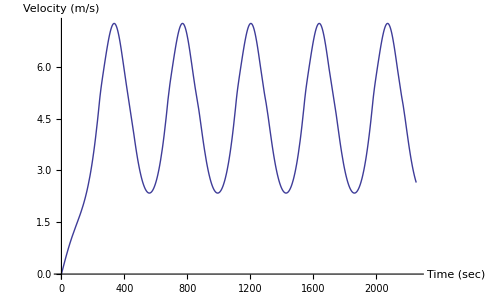

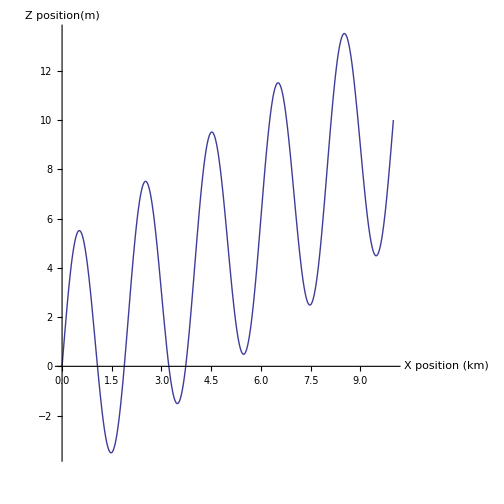

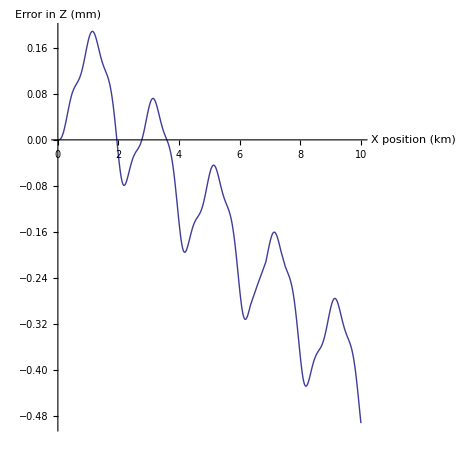

```mathematica
Plot[ xv[t],{t,0,endt},AxesLabel->{"Time (sec)", "Velocity (m/s)"}]
ParametricPlot[ {xp[t]/1000 , zp[t]},{t,0,endt},  AxesLabel->{"X position (km)", "Z position(m)"}, AspectRatio->1/1]
ParametricPlot[ {xp[t]/1000 , (zp[t]-htrack[xp[t]])*1000.},{t,0,endt},  AxesLabel->{"X position (km)", "Error in Z (mm)"}, AspectRatio->1/1]
```

We now use table and table form to have to put the positions and velocities as a function of the interval selected by the user. (The default interval is 100 seconds).  To generate the table with 100s output, and to add the final value, we generate the table in two parts and save the table in a list called outlst. We use the append function to join the two tables together.

```mathematica
outlst = Table[{t,xp[t],zp[t],xv[t],zv[t]},{t,0,endt,outint}];
(* Now add the final entry to the tabe; *)
outlst = Append[outlst,Transpose[Table[{t,xp[t],zp[t],xv[t],zv[t]},{t,endt,endt,outint}]]];
TableForm[outlst,TableHeadings->{None,{"Time (s)","X Pos (m)","Z pos (m)", "X Vel (m/s)","Z Vel (m/s)"}}]
```

Time (s) | X Pos (m) | Z pos (m) | X Vel (m/s) | Z Vel (m/s)
0 | 0. | 0. | 0. | -5.29396×10^-23
100 | 79.9901 | 1.32329 | 1.48869 | 0.0241386
200 | 306.763 | 4.41341 | 3.36696 | 0.0335387
300 | 826.797 | 3.41531 | 6.79761 | -0.0845564
400 | 1513.81 | -3.48135 | 5.87698 | 0.00988077
500 | 1951.68 | 1.19559 | 2.95947 | 0.0489105
600 | 2202.42 | 5.17194 | 2.65422 | 0.0361969
700 | 2608.52 | 7.32075 | 5.8297 | -0.0247871
800 | 3292.9 | -0.685554 | 6.88819 | -0.0586485
900 | 3834.83 | 1.35511 | 3.88251 | 0.0568391
1000 | 4117.37 | 5.91931 | 2.35353 | 0.0368374
1100 | 4428.12 | 9.30101 | 4.53331 | 0.0204786
1200 | 5046.56 | 4.31778 | 7.24973 | -0.105412
1300 | 5681.7 | 1.47426 | 4.97372 | 0.0471862
1400 | 6035.25 | 6.58758 | 2.48085 | 0.0412101
1500 | 6294.17 | 10.2845 | 3.32052 | 0.0347469
1600 | 6803.7 | 9.69517 | 6.71443 | -0.0793262
1700 | 7493.54 | 2.49435 | 5.98646 | 0.00407604
1800 | 7941.44 | 7.0264 | 3.03341 | 0.0498764
1900 | 8193.43 | 11.0479 | 2.60451 | 0.0361917
2000 | 8588.77 | 13.3952 | 5.72489 | -0.0190286
2100 | 9269.22 | 5.52648 | 6.96317 | -0.0655712
2200 | 9821.37 | 7.16001 | 3.99206 | 0.0570797
2255.17 | 10000. | 9.99951 | 2.65009 | 0.0442763

Alternative solution,  Here we solve the one dimensional problem which is basically the roller coaster solution that keeps the bike on the ground.  In the Fortran and C-versions we computed the forces along the sloped surface and integrated horizontal motions from the motion along the slope.  If  a similar approach is followed here, then we need expressions for height and slope as functions of the distance along the sirface.  These could be derived given that we have the eqautions.  A simpler solution to solve for the horizontal motion and compute the z-motion consistent wth staying on the track.  The z-motion is needed because drag and rider force depend on the total velocity not just the horizontal velocity. 
We use the same constants above but we re-define the accerations and NDSolve here.

```mathematica
theta[xp_] := ArcTan[slope + as*Cos[2*Pi*xp/lambda]*2*Pi/lambda - bs*Sin[2*Pi*xp/lambda]*2*Pi/lambda]

(* Get total velocity given running on track *)
vtot[xd_,xp_] := Sqrt[xd^2+(xd*Tan[theta[xp]])^2];

dacc[xd_, xp_] := -cd*rhoair*vtot[xd,xp]^2*area/(2*mass);
racc[th_] := -grav*cr*Cos[th];
facc[xd_,xp_]:= Min[If[ vtot[xd,xp] > 0, prider/vtot[xd,xp],fmax], fmax]/mass
gacc[th_] := -grav*Sin[th];
Print["1-D accelerations set"]
```

1-D accelerations set

```mathematica
(* Set up differential equations to be be solved, x[t] is horizontal position, There is still a problem here with along track versus horizontal distance
Here we use y for the dependent variable*)
solnb = NDSolve[{y''[t]==(dacc[y'[t],y[t]]+gacc[theta[y[t]]]+racc[theta[y[t]]]+facc[y'[t],y[t]])*Cos[theta[y[t]]],
y[0] == 0, y'[0] == 0.0},y,{t,0.0,10000.0}, AccuracyGoal->10];
py[t_]:= Evaluate[y[t]/.solnb];
vy[t_] := Evaluate[y'[t]/.solnb];
(* Compute the error in the distance *)
endb  = t /. FindRoot[py[t]-tracklen==0 ,{t,1,3000.0}];
work = NIntegrate[mass*facc[First[vy[t]],First[py[t]]]*vtot[First[vy[t]],First[py[t]]],{t,0,endt}];
Print["Time to reach end of track ",endb," sec, Speed ",First[vy[endt]]," m/s"];
Print["Work done ",work," Joules, ",work/4.1868/10^3," kcal" ];
```

Time to reach end of track 2255.05 sec, Speed 2.64848 m/s

Work done 174405. Joules, 41.6558 kcal

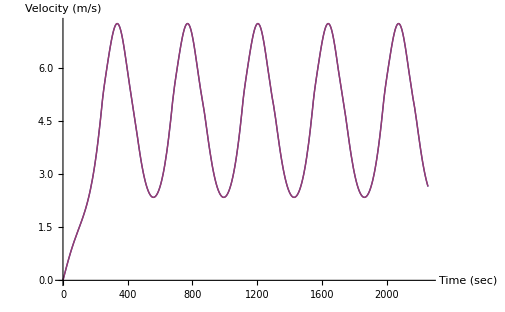

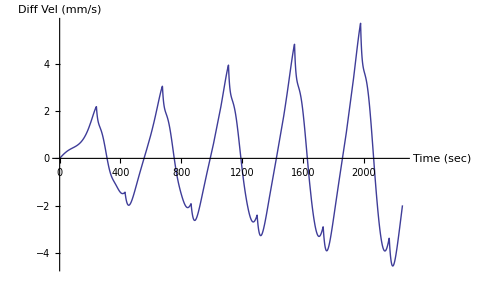

```mathematica
Plot[{vy[t],Sqrt[xv[t]^2+zv[t]^2]},{t,0,endb},PlotRange->All,AxesLabel->{"Time (sec)", "Velocity (m/s)"}]
Plot[(vy[t]-Sqrt[xv[t]^2+zv[t]^2])*1000,{t,0,endb},PlotRange->All,AxesLabel->{"Time (sec)", "Diff Vel (mm/s)"}]
```

Now output table of values

```mathematica
outl1d = Table[{t,py[t],vy[t]},{t,0,endb,outint}];
(* Now add the final entry to the tabe; *)
outl1d = Append[outl1d,Transpose[Table[{t,py[t],vy[t]},{t,endb,endb,outint}]]];
TableForm[outl1d,TableHeadings->{None,{"Time (s)","X Pos (m)","X Vel (m/s)"}}]
```

Time (s) | X Pos (m) | X Vel (m/s)
0 | 0. | 0.
100 | 80.0296 | 1.48938
200 | 306.907 | 3.36857
300 | 827.102 | 6.79856
400 | 1514.08 | 5.87554
500 | 1951.82 | 2.95863
600 | 2202.58 | 2.65548
700 | 2608.89 | 5.83165
800 | 3293.34 | 6.88692
900 | 3835.08 | 3.8804
1000 | 4117.54 | 2.35409
1100 | 4428.5 | 4.537
1200 | 5047.16 | 7.25006
1300 | 5682.12 | 4.97145
1400 | 6035.47 | 2.48028
1500 | 6294.5 | 3.32362
1600 | 6804.39 | 6.7169
1700 | 7494.16 | 5.98318
1800 | 7941.75 | 3.03121
1900 | 8193.74 | 2.6065
2000 | 8589.47 | 5.72868
2100 | 9270.08 | 6.96082
2200 | 9821.86 | 3.98801
2255.05 | 10000. | 2.65031